# Mutation-selection-drift balance with irreversible (and non-reccurent) (deleterious) mutations

## strong selection ? (ignore -- not sure where this used)

With sufficiently rare mutation (U<<1), Wright 1938 (PNAS 24:253) equation 29 with C=4U and t=0 gives the distribution of mutant allele frequency, q, as

```mathematica
f[q_]:=U Exp[4 γ q] 4/(q(1-q))
```

where U is the population scaled mutation rate (U = N u, where u is the probability of mutation per individual) and γ is the population scaled selection coefficient (γ = Ne s, where Ne is the effective population size and s is the selection coefficient of the mutant, s>0 if beneficial, s<0 if deleterious).

Thinking about a haploid population we divide N by two to get

```mathematica
f[q_]:=U Exp[2 γ q] 2/(q(1-q))
```

This looks like

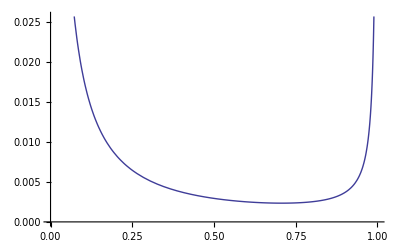

```mathematica
Plot[f[q]/.γ->s Ne/.U->u Ne/.s->-0.001/.Ne->1000/.u->10^-6,{q,0,1},PlotRange->{0,Automatic}]
```

## weak selection ? (used in bustamente et al 2001 genetics and elsewhere)

With weak sufficiently weak selection (|γ|<<1?) equation 39 in Wright 1938 gives (after converting to a haploid population by dividing N by 2)

```mathematica
f[q_]:=(1-Exp[-2 γ(1-q)])/(1-Exp[-2γ]) (2U)/(q(1-q))
```

This looks like

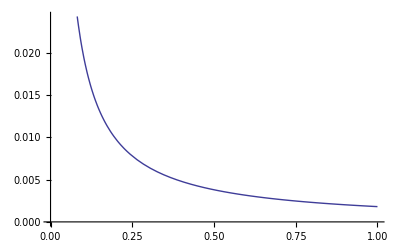

```mathematica
Plot[f[q]/.γ->s Ne/.U->u Ne/.s->-0.0001/.Ne->1000/.u->10^-6,{q,0,1},PlotRange->{0,Automatic}]
```

We are actually more interested in the probability that a mutation that is segregating is sampled at frequency q. From equation 1 in Bustamante et al 2001 (Genetics 159:1779), this is

```mathematica
f[q_]:=(1-Exp[-2 γ(1-q)])/(1-Exp[-2γ]) 2/(q(1-q))
```

which is just the previous f[q] with U=1 (ie once the mutation has occured we no longer need to consider the rate at which it appears as we only consider it to appear once).

This looks like:

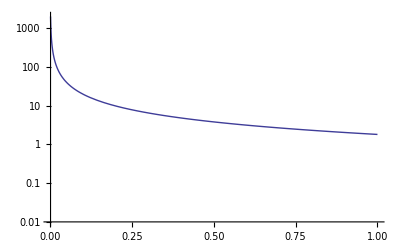

```mathematica
LogPlot[f[q]/.γ->s Ne/.s->-0.0001/.Ne->1000,{q,1/1000,1},PlotRange->{10^-2,All}]
```

If this mutation is not lost or fixed (note that f[q] is not well-defined at these points) the PDF is

```mathematica
f[q]/Integrate[f[q],{q,1/n,1-1/n},Assumptions->n>2]
```

((-1+ⅇ^(2 γ)) (1-ⅇ^(-2 (1-q) γ)))/((1-ⅇ^(-2 γ)) (1-q) q (ⅇ^(2 γ) ExpIntegralEi[-(2 γ)/n]+ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]-ExpIntegralEi[(2 (-1+n) γ)/n]+2 ⅇ^(2 γ) Log[-1+n]))

lets call that g

```mathematica
g[q_]:=((-1+ⅇ^(2 γ)) (1-ⅇ^(-2 (1-q) γ)))/((1-ⅇ^(-2 γ)) (1-q) q (ⅇ^(2 γ) ExpIntegralEi[-(2 γ)/n]+ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]-ExpIntegralEi[(2 (-1+n) γ)/n]+2 ⅇ^(2 γ) Log[-1+n]))
```

We next want to get the CDF from the above PDF (for the inverse transform sampling method, in order to pull random numbers from this distribution)

```mathematica
Integrate[g[q],{q,1/n,x},Assumptions->{0<n,1/n<x<1}]
```

(ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]+ⅇ^(2 γ) ExpIntegralEi[2 (-1+x) γ]-ExpIntegralEi[2 x γ]+ⅇ^(2 γ) Log[-1+n]+ⅇ^(2 γ) Log[-x/(-1+x)])/(ⅇ^(2 γ) ExpIntegralEi[-(2 γ)/n]+ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]-ExpIntegralEi[(2 (-1+n) γ)/n]+2 ⅇ^(2 γ) Log[-1+n])

```mathematica
cdf[x_]:=(ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]+ⅇ^(2 γ) ExpIntegralEi[2 (-1+x) γ]-ExpIntegralEi[2 x γ]+ⅇ^(2 γ) Log[-1+n]+ⅇ^(2 γ) Log[-x/(-1+x)])/(ⅇ^(2 γ) ExpIntegralEi[-(2 γ)/n]+ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]-ExpIntegralEi[(2 (-1+n) γ)/n]+2 ⅇ^(2 γ) Log[-1+n])
```

```mathematica
FullSimplify[cdf[x],{n>2,γ<0,0<x<1}]
```

(ExpIntegralEi[(2 γ)/n]-ExpIntegralEi[2 x γ]+ⅇ^(2 γ) (-ExpIntegralEi[2 (-1+1/n) γ]+ExpIntegralEi[2 (-1+x) γ]+Log[-((-1+n) x)/(-1+x)]))/(ExpIntegralEi[(2 γ)/n]-ExpIntegralEi[(2 (-1+n) γ)/n]+ⅇ^(2 γ) (-ExpIntegralEi[2 (-1+1/n) γ]+ExpIntegralEi[-(2 γ)/n]+2 Log[-1+n]))

```mathematica
?ExpIntegralEi
```

ExpIntegralEi[z] gives the exponential integral function Ei(z).

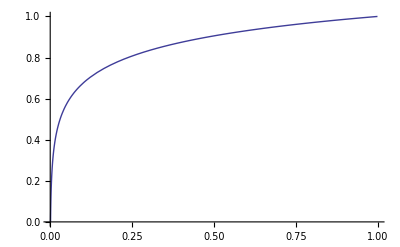

```mathematica
Plot[cdf[x]/.γ->-0.1/.n->1000,{x,1/1000,1-1/1000},PlotRange->{0,All}]
```

we can then use the inverse transform method to sample from the pdf (choose a random number u uniformly from (0,1) and calculate what x solves cdf[x] = u)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

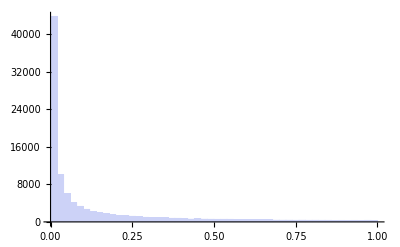

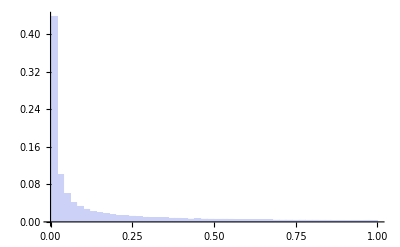

0.140115

```mathematica
nnums=10^5;
Table[Random[Real],{x,nnums}];
Table[x/.FindRoot[cdf[x]-rv/.rv->%[[i]]/.γ->-0.1/.n->1000,{x,0.5}],{i,1,nnums}];
Histogram[%,Automatic]
Histogram[%%,Automatic,"Probability"]
Mean[%%%]
```

and we see this matches the shape of the pdf (y-axis numbers do not align... trying to figure out how to make this happen -- something to do with finite sample??)

```mathematica
NIntegrate[g[q]/.γ->-0.1/.n->1000,{q,1/1000,1-1/1000}]
```

1.

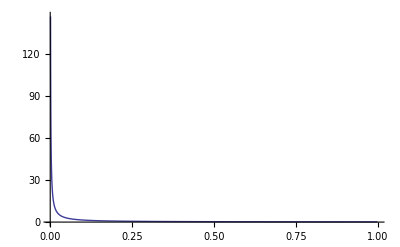

```mathematica
Plot[g[q]/.γ->-0.1/.n->1000,{q,1/1000,1-1/1000},PlotRange->All]
```

try to get expected value...

```mathematica
Integrate[q g[q],{q,0+1/n,1-1/n},Assumptions->n>2]
```

(ⅇ^(2 γ) (-ExpIntegralEi[2 (-1+1/n) γ]+ExpIntegralEi[-(2 γ)/n]+Log[-1+n]))/(ⅇ^(2 γ) ExpIntegralEi[-(2 γ)/n]+ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]-ExpIntegralEi[(2 (-1+n) γ)/n]+2 ⅇ^(2 γ) Log[-1+n])

```mathematica
(ⅇ^(2 γ) (-ExpIntegralEi[2 (-1+1/n) γ]+ExpIntegralEi[-(2 γ)/n]+Log[-1+n]))/(ⅇ^(2 γ) ExpIntegralEi[-(2 γ)/n]+ExpIntegralEi[(2 γ)/n]-ⅇ^(2 γ) ExpIntegralEi[-(2 (-1+n) γ)/n]-ExpIntegralEi[(2 (-1+n) γ)/n]+2 ⅇ^(2 γ) Log[-1+n])/.n->1000/.γ->-0.1
```

0.139368